## Order Stuff

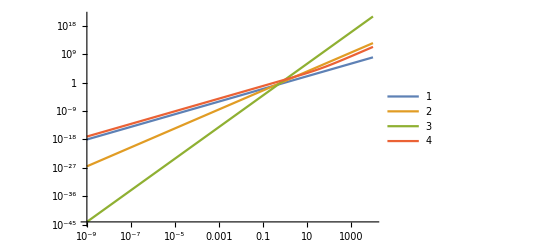

```mathematica
g3[h_]:= 3.2 h^3
g5[h_]:= 8.5 h^5
gX[h_]:= 8.5 h^2+ 0.2 h^3
LogLogPlot[ {h^2,g3[h],g5[h],gX[h]},{h, 10^-9, 10000},
PlotLegends->Automatic]
```

# Equilibrium And Stability

We want to understand the equilibrium points and their linear stability for the Rosseler System.  We are going to start with a 2D problem because it will be easier to draw and understand pictures.  We will check our understanding as we go.  Lets look at the van der Pol system.  https://en.wikipedia.org/wiki/Van_der_Pol_oscillator

### Van Der Pol System

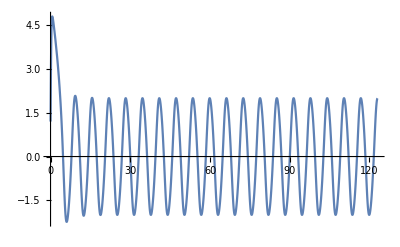

```mathematica
TMax=123; μ=0.3;
xSol = NDSolveValue[{
x''[t]-μ (1-x[t]^2)x'[t]+x[t]==0,
x[0]==1.2, x'[0]==12.3},x,{t, 0, TMax}] ;
Plot[xSol[t],{t,0, TMax}]
```

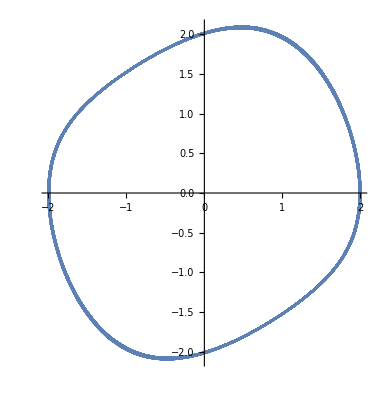

```mathematica
Clear[xvSol]
TMax=1234; μ=0.3;
xvSol[t_] = NDSolveValue[{
x'[t]==v[t],
v'[t]==μ (1-x[t]^2)v[t]-x[t],
x[0]==1.2, v[0]==2.3},{x[t],v[t]},{t, 0, TMax}] ;
ParametricPlot[xvSol[t],{t,1/2 TMax, TMax}]
```

```mathematica
Clear[pSol]
TMax=200; μ=0.3;
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
pSol = NDSolveValue[{
p'[t]==f[μ][p[t]],
p[0]==0.00000001{1.2,2.3}},p,{t, 0, TMax}] 
Pic = ParametricPlot[pSol[t],{t,0, TMax},
PlotRange->All]
```

```mathematica
A[μ_][{x_,v_}]:={{0,1},
{-2μ x v-1,μ (1-x^2)}
}
Clear[μ]
D[ μ (1-x^2)v-x,{{x,v}}]
```

{-1-2 v x μ,(1-x^2) μ}

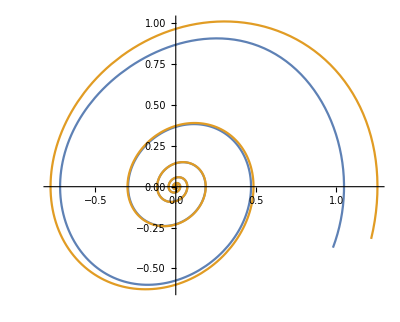

```mathematica
μ=0.3;
A0=A[μ][{0,0}];
TMax=123;
pSol = NDSolveValue[{
p'[t]==f[μ][p[t]],
p[0]==0.00000001{1.2,2.3}},p,{t, 0, TMax}] ;
wSol = NDSolveValue[{
p'[t]==A0.p[t],
p[0]==0.00000001{1.2,2.3}},p,{t, 0, TMax}] ;
Pic = ParametricPlot[{pSol[t],wSol[t]},{t,0, TMax},
PlotRange->All]
```

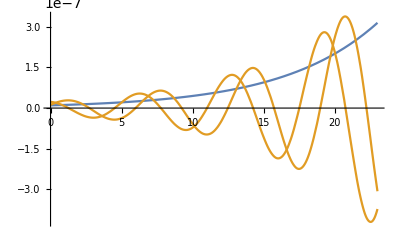

```mathematica
Plot[ {0.00000001 E^(0.15 t),wSol[t]},{t,0, 23}]
```

The point is that the linearization tells us what the system does near equilibrium points.  We will see that we can sort of paste multiple equilibrium points together to see the big picture.

# Rosseler System

Here is the system.

```mathematica
{a,b,c}={0.2,0.2,5.6};
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
TMax=150;
```

```mathematica
sol = NDSolveValue[{xyz'[t]==f[xyz[t]],xyz[0]=={0.2,0.4,13.4}},xyz,{t,0, TMax}]
Pic=ParametricPlot3D[sol[t],{t,0,TMax},
PlotPoints->200,
PlotRange->All,
PlotStyle->Thin]
```

InterpolatingFunction[{{0., 150.}}, <>]

-Graphics3D-

Lets find the equilibrium points.  Since f is a simple polynomial we can solve analytically.  We could also do it by hand!

```mathematica
pts=Solve[f[{x,y,z}]=={0,0,0}]
Show[Pic,Graphics3D[{Red, PointSize[0.02],Point[{x,y,z}/.pts]}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.00715199,y→-0.03576,z→0.03576},{x→5.59285,y→-27.9642,z→27.9642}}

-Graphics3D-

```mathematica
{{x->0.007026204834100129,y->-0.035131024170500645,z->0.035131024170500645},{x->5.6929737951659,y->-28.4648689758295,z->28.4648689758295}}
```

-Graphics3D-

```mathematica
f[{x,y,z}]=={0,0,0}
```

{-y-z,x+0.2 y,0.2+(-5.7+x) z}=={0,0,0}

Brief interlude to solve on the board!

Once we have the equilibrium points we can plug into the derivative and compute the eigenvalues to see what happens at the equilibrium points.

```mathematica
GradRoss = D[f[{x,y,z}],{{x,y,z}}];
MatrixForm[GradRoss]
Map[Eigenvalues,GradRoss/.pts]
```

(0 | -1 | -1
1 | 0.2 | 0
z | 0 | -5.6+x)

{{-5.58664+0. ⅈ,0.0968955+0.99521 ⅈ,0.0968955-0.99521 ⅈ},{-4.75602×10^-6+5.38171 ⅈ,-4.75602×10^-6-5.38171 ⅈ,0.192858+0. ⅈ}}

Lets stop and think about what we expect to see if we start near the “surprise” second CP 
	{5.69297,-28.4649,28.4649}
we should spiral in slowly towards an axis while being blasted out along the axis

```mathematica
{a,b,c}={0.2,0.2,5.7};
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
TMax=150;
sol = NDSolveValue[{p'[t]==f[p[t]],p[0]=={5.6,-28.4,28.4}},p,{t,0, TMax}];
pts={
{x->0.007026204834100129,y->-0.035131024170500645,z->0.035131024170500645},{x->5.6929737951659,y->-28.4648689758295,z->28.4648689758295}};
Show[
ParametricPlot3D[sol[t],{t,0,TMax},
PlotPoints->200,
PlotStyle->Thin],
Graphics3D[ {Red, PointSize[0.02],Point[{x,y,z}/.pts]}]]
```